```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
```

/home/zack/oscillators/faraday

Single run plots

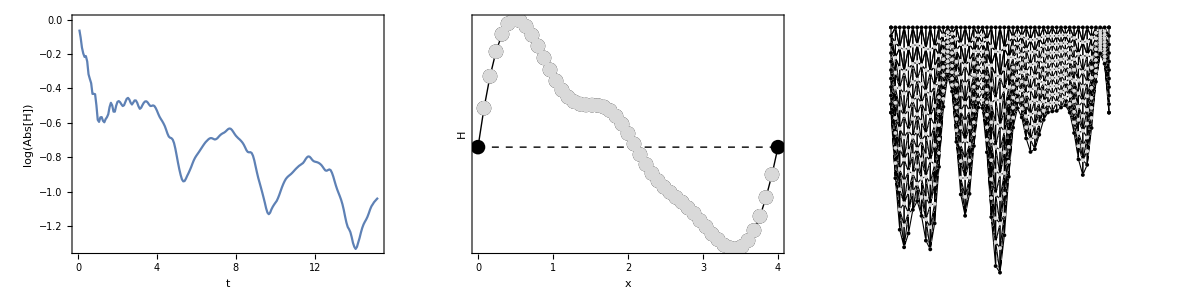

24.000000 1.000000

```mathematica
filebase="data/test";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-1;
mesh2=mesh[[m]];
Grid[{{ListPlot[Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{{0,0},{length,0}}},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[All,All,2]]],Max[mesh[[All,All,2]]]}}]}}]
lst[[-1]]
```

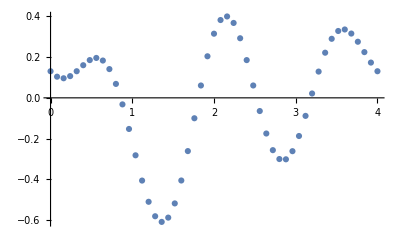

0.4

InterpolatingFunction[…]

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{0.,-0.242425,0.218733,-0.253518,-1.25818×10^-6}

{-0.0000218583,0.269666,0.445989,-0.454061,-0.0000211288}

-0.0000218583

```mathematica
ListPlot[mesh[[1,bottom]]]
Max[mesh[[1,bottom,2]]]
h=Interpolation[mesh[[1,bottom]]]
Table[NIntegrate[h[x]*Sin[n*2*Pi*x/length],{x,0,length}],{n,0,4}]
Table[NIntegrate[h[x]*Cos[n*2*Pi*x/length],{x,0,length}],{n,0,4}]
NIntegrate[h[x],{x,0,length}]
```

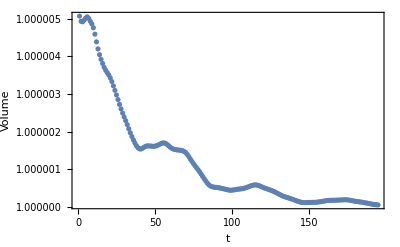

```mathematica
(* Numerical loss of fluid volume during saturation, but not too bad...*)
ListPlot[Total[#[[top,2]]]/(Length[top]*height)&/@mesh,Axes->False,Frame->True,FrameLabel->{t,"Volume"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]
```

```mathematica
modes=Table[2*Pi*n/length,{n,1,20}]
frequencies=2*(980*modes*Tanh[height*modes]*(1+72/980*modes^2))^(1/2)/(2*Pi)
modes2=Table[Pi*n/length,{n,1,20}]
frequencies2=2*(980*modes2*Tanh[height*modes2]*(1+72/980*modes2^2))^(1/2)/(2*Pi)
```

{1.5708,3.14159,4.71239,6.28319,7.85398,9.42478,10.9956,12.5664,14.1372,15.708,17.2788,18.8496,20.4204,21.9911,23.5619,25.1327,26.7035,28.2743,29.8451,31.4159}

{10.9922,22.2161,34.7764,49.2379,65.6567,83.9163,103.873,125.396,148.377,172.725,198.365,225.233,253.271,282.433,312.675,343.958,376.249,409.516,443.731,478.868}

{0.785398,1.5708,2.35619,3.14159,3.92699,4.71239,5.49779,6.28319,7.06858,7.85398,8.63938,9.42478,10.2102,10.9956,11.781,12.5664,13.3518,14.1372,14.9226,15.708}

{5.51932,10.9922,16.5031,22.2161,28.2768,34.7764,41.7591,49.2379,57.2083,65.6567,74.5655,83.9163,93.691,103.873,114.446,125.396,136.71,148.377,160.385,172.725}

Generate box substrate

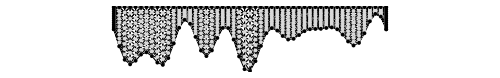

```mathematica
filebase="data/test";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-1;
mesh2=mesh[[m]];
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[All,All,2]]],Max[mesh[[All,All,2]]]}}]
```

```mathematica
modes[[1]]
```

-0.0663824

```mathematica
modes=ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate modes"][[1]]+1]]]];
smodes=Length[modes]/2;
subss=ConstantArray[0.,{smodes,smodes}]
subsc=Normal[SparseArray[Table[{i,1}->modes[[i]],{i,1,smodes}],{smodes,smodes}]]
subcs=ConstantArray[0.,{smodes,smodes}]
subcc=Normal[SparseArray[Table[{i,1}->modes[[smodes+i]],{i,1,smodes}],{smodes,smodes}]]
file=OpenWrite["boxsubstrate.dat"]
WriteString[file,smodes]
WriteString[file,"\n"]
Do[Do[WriteString[file,subss[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subsc[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subcs[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subcc[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Close[file]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{{-0.0663824,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.399909,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.282595,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.250992,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.082586,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.0646444,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.236438,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.37809,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.0469519,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.241519,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.374609,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.153858,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.315685,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-0.368756,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0.302514,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

OutputStream[…]

boxsubstrate.dat

Animation

```mathematica
m0=Length[mesh]-500;
m1=Length[mesh];
If[!DirectoryQ["rectangleanimation"],CreateDirectory["rectangleanimation"]];
Monitor[Do[
acc=ToExpression[StringSplit[lst[[-1]]," "]][[2]];
freq=ToExpression[StringSplit[lst[[-1]]," "]][[1]];
amp=980*acc/(2*Pi*freq)^2;
z0=amp*Sin[2*Pi*m/15];
mesh2={#[[1]],z0+#[[2]]}&/@mesh[[m]];
p=Grid[{{ListPlot[{Transpose[{Range[Length[norms]]/15,Log[norms]/Log[10]}],Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}]},Joined->True,PlotStyle->{Directive[AbsoluteThickness[1],LightGray],Directive[AbsoluteThickness[2],Black]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]]},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(height+2)/(length+2),PlotRange->{{-1,length+1},{-1,height+1}}]}}];
Export["rectangleanimation/"<>IntegerString[m-m0,10,4]<>".png",p,ImageResolution->100];,{m,m0,m1}],N[(m-m0)/(m1-m0)]]
```

Periodic sweep plots

sweeps/nr9

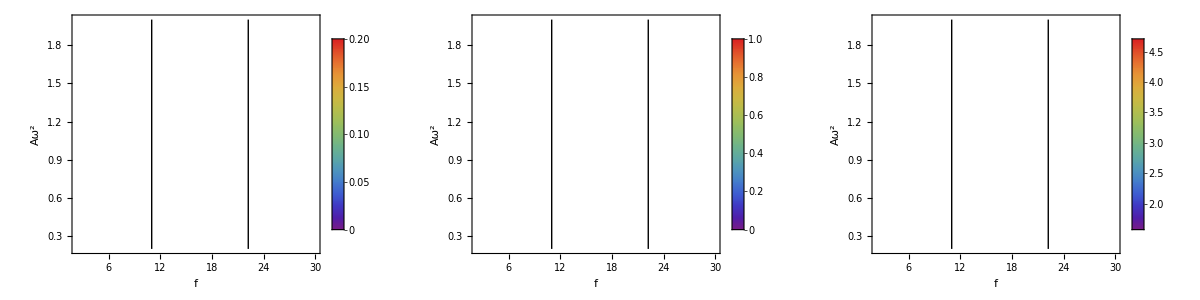

```mathematica
filebase="sweeps/nr9"
growth1=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1];
Amin=Min[growth1[[All,2]]];
Amax=Max[growth1[[All,2]]];
fmin=Min[growth1[[All,1]]];
fmax=Max[growth1[[All,1]]];
kmin=Min[growth1[[All,5]]];
kmax=Max[growth1[[All,5]]];
max=Max[growth1[[All,4]]];
ν1=2;
ν2=0;
ν3=0.5;
g=980;
σ=72;
p1=Grid[{{Show[rasterizeBackground[Show[ListDensityPlot[growth1[[All,{1,2,4}]],InterpolationOrder->0,PlotRange->{All,All,{0.0,max}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Growth Rate"}},Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]}],Plot[2*(ν1+ν3*k^2+ν2*k*Tanh[k*height])*(1+σ/g*k^2)/(k*Tanh[k*height]*(g+σ*k^2))^(1/2)/.FindRoot[2*Pi*f/2==(k*Tanh[k*height]*(g+σ*k^2))^(1/2), {k,1.0}],{f,fmin,fmax},PlotStyle->Directive[Black]]]],Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},PlotRangeClipping->False,ImageSize->400,ImagePadding->{{65,100},{50,50}}],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,3}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.0,1.1}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/1.0]&),ColorFunctionScaling->False,FrameLabel->{{Aω^2,None},{f,"Frequency"}},ImageSize->300],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,5}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
```

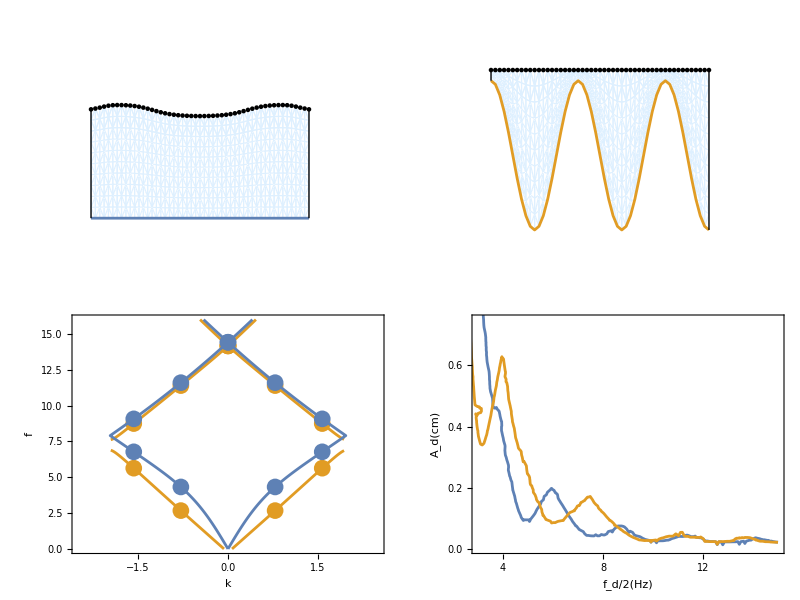

plots/periodicrectanglegap.pdf

```mathematica
gap=2*Pi/length*5/4;
ks=2*gap;
hs=1.75;
M2=4;
κ[k_, n_]:=k+n*ks;
ν1=2;
ν2=0;
ν3=0.5;
g=980;
σ=72;
ρ=1;
H1[k_,A_]:=Table[Exp[-κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])-Exp[κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H2[k_,A_]:=-Table[Exp[-κ[k,n]*height]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])+Exp[κ[k,n]*height]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H3[k_,A_]:=Table[1.0/Cosh[κ[k,n]*height]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2}];
sys[k_,A_]:={H3[k,A].H1[k,A],H3[k,A].H2[k,A]};
p1=Show[ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,-ks/2+0.01,ks/2-0.01,ks/200}]],Joined->True,Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]],ListPlot[Join[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,0,ks/2,Pi/length}]],Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,0,-ks/2,-Pi/length}]]],Joined->False,Axes->False,Frame->True,FrameLabel->{k,f},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},PlotStyle->Directive[PointSize[0.04],ColorData[97,"ColorList"][[2]]]],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}]},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2.0]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-2,2,1}],Table[{i,""},{i,-2,2,1}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},RotateLabel->True],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,Pi/length,6*Pi/length,Pi/length}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,Pi/length,6*Pi/length,Pi/length}]},Joined->False,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]]]];
filebases={"sweeps/sr3","sweeps/sr4"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
interpolations[f_,a_]=Table[Interpolation[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],InterpolationOrder->1][f,a],{i,1,Length[sweeps]}];p3=Show@@Table[ContourPlot[interpolations[f,a][[i]],{f,2.63,15},{a,0.000552,1.8},Contours->{0.0},PlotRange->{{3,15},{0,0.75}},ContourShading->None,ContourStyle->{Directive[ColorData[97,"ColorList"][[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.6,0.2}],Table[{i,""},{i,0,0.6,0.2}]},{Table[{i,i},{i,4,14,2}],Table[{i,""},{i,4,14,2}]}}],{i,1,Length[sweeps]}];
filebase="data/rectangleinhomogeneous";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
p2=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(2+Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{-1+Min[mesh[[All,All,2]]],1+Max[mesh[[All,All,2]]]}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,1.75},{0,2.0}}],Line[{{length,-1.75},{length,2.0}}]}];
filebase="data/rectanglehomogeneous";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-50;
mesh2=mesh[[m]];
p4=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(2+Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{-1+Min[mesh[[All,All,2]]],1+Max[mesh[[All,All,2]]]}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,2.0}}],Line[{{length,0},{length,2.0}}]}];
filebase="sweeps/sa1";
fsweeps=Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}];
p5=ListPlot[Table[{1.75*i/100,MinimalBy[Cases[fsweeps[[All,i]],u_/;u[[4]]>0],#[[2]]&][[1,2]]*980/(2*Pi*16)^2},{i,1,100}],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],AspectRatio->1,LabelStyle->Directive[14,Black],FrameLabel->{Subscript[A,s],Subsuperscript[A,d,c]},ImageSize->150,PlotStyle->Directive[Black],FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.1,0.05}],Table[{i,""},{i,0,0.1,0.05}]},{Table[{i,PaddedForm[i,{2,2}]},{i,0,1.75,0.75}],Table[{i,""},{i,0,1.75,0.75}]}}];
filebase="sweeps/sa3";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p5=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->150,AspectRatio->1,PlotRange->{5,8},PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[4]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[5]]]}];
p=Grid[{{p4,p2},{p1,Show[p3,Epilog->Inset[p5,{10,0.4}]]}}]
Export["plots/periodicrectanglegap.pdf",p]
```

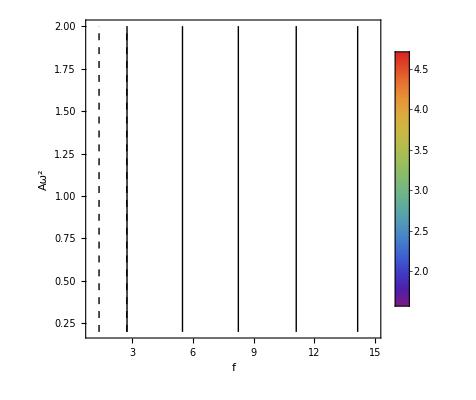
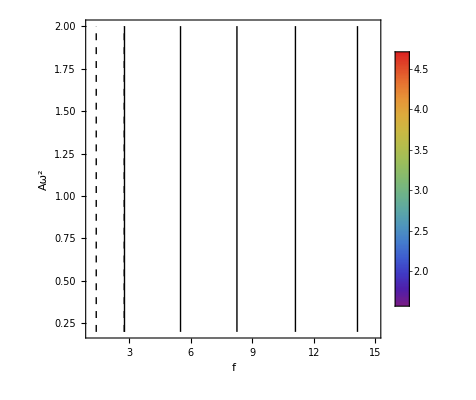

```mathematica
filebases={"sweeps/nr8","sweeps/nr9"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
Amin=Min[sweeps[[1,All,2]]];
Amax=Max[sweeps[[1,All,2]]];
fmin=Min[sweeps[[1,All,1]]];
fmax=Max[sweeps[[1,All,1]]];
kmin=Min[sweeps[[1,All,5]]];
kmax=Max[sweeps[[1,All,5]]];
max=Max[sweeps[[1,All,4]]];
p1=Table[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}]
```

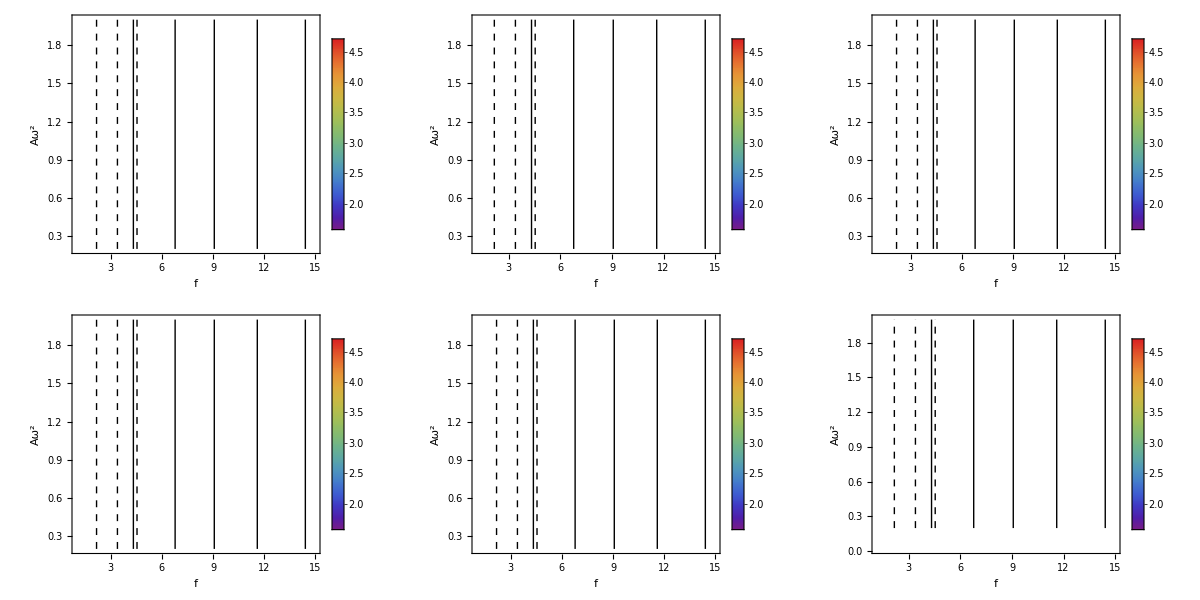

```mathematica
filebases={"sweeps/nr1","sweeps/nr1"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
Amin=Min[sweeps[[1,All,2]]];
Amax=Max[sweeps[[1,All,2]]];
fmin=Min[sweeps[[1,All,1]]];
fmax=Max[sweeps[[1,All,1]]];
kmin=Min[sweeps[[1,All,5]]];
kmax=Max[sweeps[[1,All,5]]];
max=Max[sweeps[[1,All,4]]];
p1=Table[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}];
filebases={"sweeps/nr3","sweeps/nr4"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p2=Table[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}];
filebases={"sweeps/nr5","sweeps/r2"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p3=Table[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}];
p=Grid[Transpose[{p1,p2,p3}]]
```

Random substrates

```mathematica
Clear[mins]
Clear[maxes]
filebases={"sweeps/nr8","sweeps/nr9"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
filebase="sweeps/r3";
random=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
seeds=Flatten[DeleteDuplicates/@random[[All,All,7]]];
wavenumbers=DeleteDuplicates[Flatten[(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6]&/@random)[[All,All,5]]]];
maxes[case_]:=Max/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
mins[case_]:=Min/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
gaps=(mins/@wavenumbers[[2;;-1]])-(maxes/@wavenumbers[[1;;-2]]);
shifts=Transpose[#-gaps[[All,1]]&/@(Transpose[gaps])];
ListPlot[shifts,ImageSize->500,PlotRange->{-1,5}]
Reverse[SortBy[seeds,Total[shifts[[1;;4,First@FirstPosition[seeds,#]]]]&]]
min=First@MinimalBy[Sort[DeleteDuplicates[sweeps[[1,All,2]]]],Abs[#-0.8]&];
ListPlot[{{#[[1]],#[[2]]-0.1}&/@Cases[sweeps[[1]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],Cases[random[[71]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.1}&/@Cases[sweeps[[2]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]]},PlotRange->{{0,30},{0,5}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"f","k"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]],AspectRatio->1,PlotStyle->Directive[PointSize[0.03]],PlotLegends->{"Homogeneous","Best random","Periodic"}]
```

Part::take: Cannot take positions 2 through -1 in {}.

Part::take: Cannot take positions 1 through -2 in {}.

Transpose::nmtx: The first two levels of {} cannot be transposed.

ListPlot::lpn: Transpose[Transpose[{}]] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Transpose[Transpose[{}]],ImageSize→500,PlotRange→{-1,5}]

{}

Part::partw: Part 71 of {} does not exist.

Part::partw: Part 4 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd: Part specification 71⟦4⟧ is longer than depth of object.

Part::partd: Part specification 71⟦3⟧ is longer than depth of object.

ListPlot::lpn: «1» is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{{{5.67677,1.4708},{5.9596,1.4708},{6.24242,1.4708},{6.52525,1.4708},{6.80808,1.4708},{7.09091,1.4708},{11.0505,2.25619},{11.3333,2.25619},{11.6162,2.25619},{11.899,2.25619},{12.1818,2.25619},{12.4646,2.25619},{12.7475,2.25619},{13.0303,2.25619},{13.3131,2.25619},{13.596,2.25619},{13.8788,2.25619},{16.9899,3.04159},{17.2727,3.04159},{17.5556,3.04159},{17.8384,3.04159},{18.1212,3.04159},{18.404,3.04159},{18.6869,3.04159},{18.9697,3.04159},{19.2525,3.04159},{19.5354,3.04159},{19.8182,3.04159},{20.101,3.04159},{20.3838,3.04159},{23.2121,3.82699},{23.4949,3.82699},{23.7778,3.82699},{24.0606,3.82699},{24.3434,3.82699},{24.6263,3.82699},{30.,4.61239}},{},{{4.26263,1.6708},{4.54546,1.6708},{4.82828,1.6708},{7.93939,2.45619},{8.22222,2.45619},{8.50505,2.45619},{8.78788,2.45619},{9.07071,2.45619},{9.35354,2.45619},{9.63636,2.45619},{16.4242,3.24159},{16.7071,3.24159},{16.9899,3.24159},{17.2727,3.24159},{17.5556,3.24159},{17.8384,3.24159},{18.1212,3.24159},{18.404,3.24159},{18.6869,3.24159},{18.9697,3.24159},{19.2525,3.24159},{19.5354,3.24159},{19.8182,3.24159},{22.6465,4.02699},{22.9293,4.02699},{23.2121,4.02699},{23.4949,4.02699},{23.7778,4.02699},{24.0606,4.02699}}},PlotRange→{{0,30},{0,5}},ImageSize→300,Axes→False,Frame→True,FrameLabel→{f,k},LabelStyle→Directive[16,GrayLevel[0]],FrameStyle→Directive[GrayLevel[0],AbsoluteThickness[1]],AspectRatio→1,PlotStyle→Directive[PointSize[0.03]],PlotLegends→{Homogeneous,Best random,Periodic}]

{1.5708,2.35619,3.14159,3.92699,4.71239}

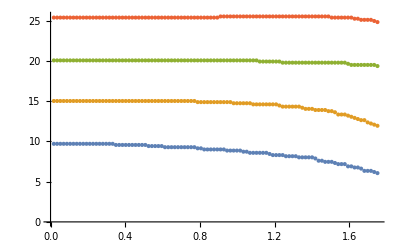

```mathematica
(*Find the gaps between tongues here, and plot as a function of samp *)
filebase="sweeps/sa3";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
wavenumbers=DeleteDuplicates[Flatten[(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6]&/@fsweeps)[[All,All,5]]]]
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers[[1;;4]]}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers[[1;;4]]}];
means=(mins+maxes)/2;
ListPlot[means]
```

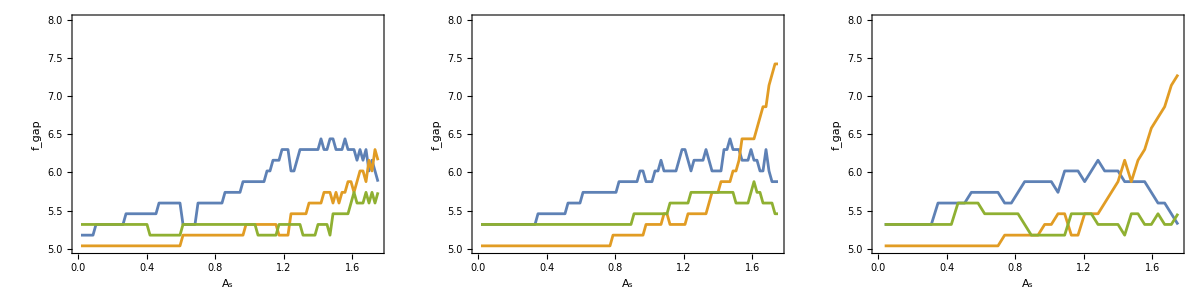

```mathematica
filebase="sweeps/sa2";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p1=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotRange->{5,8},PlotStyle->Directive[AbsoluteThickness[2]]];

filebase="sweeps/sa3";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p2=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotRange->{5,8},PlotStyle->Directive[AbsoluteThickness[2]]];

filebase="sweeps/sa4";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p3=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->300,AspectRatio->1,PlotRange->{5,8},PlotStyle->Directive[AbsoluteThickness[2]]];
Grid[{{p1,p2,p3}}]
```

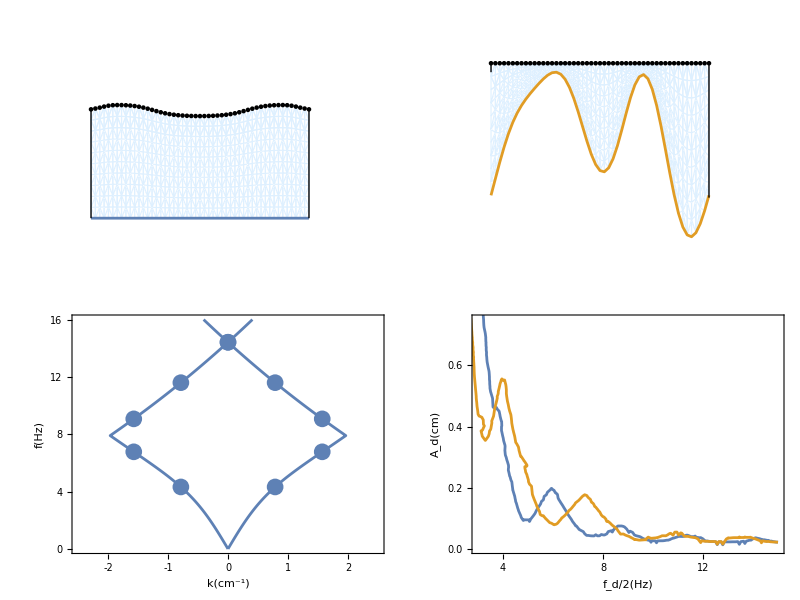

plots/randomrectanglegap.pdf

```mathematica
gap=2*Pi/length*5/4;
ks=2*gap;
hs=1.75;
M2=4;
κ[k_, n_]:=k+n*ks;
ν1=2;
ν2=0;
ν3=0.5;
g=980;
σ=72;
ρ=1;
H1[k_,A_]:=Table[Exp[-κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])-Exp[κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H2[k_,A_]:=-Table[Exp[-κ[k,n]*height]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])+Exp[κ[k,n]*height]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H3[k_,A_]:=Table[1.0/Cosh[κ[k,n]*height]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2}];
sys[k_,A_]:={H3[k,A].H1[k,A],H3[k,A].H2[k,A]};
p1=Show[ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}]},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2.0]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-2,2,1}],Table[{i,""},{i,-2,2,1}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},RotateLabel->True],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,Pi/length,6*Pi/length,Pi/length}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,Pi/length,6*Pi/length,Pi/length}]},Joined->False,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]]]];
filebases={"sweeps/sr3","sweeps/r2"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
interpolations[f_,a_]=Table[Interpolation[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],InterpolationOrder->1][f,a],{i,1,Length[sweeps]}];p3=Show@@Table[ContourPlot[interpolations[f,a][[i]],{f,2.63,15},{a,0.000552,1.8},Contours->{0.0},PlotRange->{{3,15},{0,0.75}},ContourShading->None,ContourStyle->{Directive[ColorData[97,"ColorList"][[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0,0.6,0.2}],Table[{i,""},{i,0,0.6,0.2}]},{Table[{i,i},{i,4,14,2}],Table[{i,""},{i,4,14,2}]}}],{i,1,Length[sweeps]}];
filebase="data/rectanglerandom";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
p2=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(2+Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{-1+Min[mesh[[All,All,2]]],1+Max[mesh[[All,All,2]]]}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,1.75},{0,2.0}}],Line[{{length,-1.75},{length,2.0}}]}];
filebase="data/rectanglehomogeneous";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-50;
mesh2=mesh[[m]];
p4=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(2+Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{-1+Min[mesh[[All,All,2]]],1+Max[mesh[[All,All,2]]]}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,2.0}}],Line[{{length,0},{length,2.0}}]}];
filebase="sweeps/sa4";
fsweeps=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],{}];
substrates=Flatten[DeleteDuplicates[fsweeps[[All,All,6]]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[fsweeps,1][[All,5]]]][[1;;4]];
mins=Table[MinimalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
maxes=Table[MaximalBy[#,#[[1]]&][[1,{6,1}]]&/@(Cases[#,u_/;u[[4]]>0.5&&u[[3]]<0.6&&u[[5]]==wavenumber]&/@Transpose[fsweeps]),{wavenumber,wavenumbers}];
means=(mins+maxes)/2;
p5=ListPlot[{Transpose[{means[[2,All,1]],means[[2,All,2]]-means[[1,All,2]]}],Transpose[{means[[3,All,1]],means[[3,All,2]]-means[[2,All,2]]}],Transpose[{means[[4,All,1]],means[[4,All,2]]-means[[3,All,2]]}]},Joined->True,Axes->False,Frame->True,FrameLabel->{Subscript[A,s],Subscript[f,"gap"]},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->150,AspectRatio->1,PlotRange->{5,8},PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[4]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[5]]]}];
p=Grid[{{p4,p2},{p1,Show[p3,Epilog->Inset[p5,{10,0.4}]]}}]
Export["plots/randomrectanglegap.pdf",p]
```

Flat substrate Floquet predictions

```mathematica
rate[k_,ω_,A_,ν_]:=Module[{t0,t1,sol,norms,maxes},
t0=2*Pi*25;
t1=2*Pi*50;
sol=First@NDSolve[{ω^2*h''[t]==k*Tanh[k]*((-1+A*ω*Sin[t])*h[t]-ν*ω*h'[t]), h[0]==0.001, h'[0]==0}, h[t], {t,0,t1}];
norms=Table[h[t]/.sol,{t,t0,t1,2*Pi*0.1}];
maxes=First/@Position[Differences[Sign[Differences[norms]]],-2];
If[Mean[Log[Abs[norms]]]/Log[10]<-5,{k,ω,A,1/(0.1*Mean[Differences[maxes]]),-1,norms},{k,ω,A,1/(0.1*Mean[Differences[maxes]]),D[ω*Fit[Transpose[{2*Pi*0.1*maxes,Log[Abs[norms[[maxes]]]]}][[Ceiling[Length[maxes]/2];;-1]],{1,x},x],x],norms}]]
ωmin=1.5;
ωmax=3.0;
Amin=0.0;
Amax=0.3;
ν=0.05;
M=50;
AbsoluteTiming[Monitor[rates=Flatten[Table[First@MaximalBy[Table[rate[k,ω,A,ν][[1;;5]],{k,modes}],#[[5]]&],{ω,ωmin,ωmax,(ωmax-ωmin)/M},{A,Amin,Amax,(Amax-Amin)/M}],1];,N[{(ω-ωmin)/(ωmax-ωmin),(A-Amin)/(Amax-Amin)}]]]
```

{48.6212,Null}

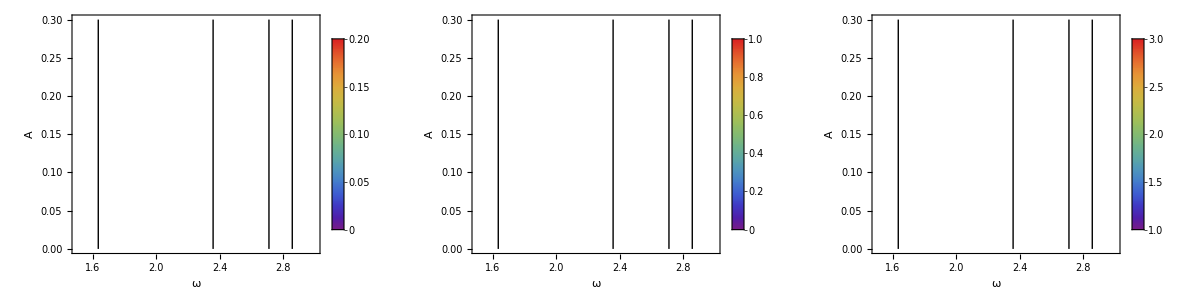

plots/benchmark.pdf

```mathematica
p2=Grid[{{rasterizeBackground[Show[ListDensityPlot[rates[[All,{2,3,5}]],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],PlotRange->{0,0.2},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/0.2]&), FrameLabel->{{A,None},{ω,"Growth Rate"}},ClippingStyle->None],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,4}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/1]&),PlotRange->{0,1.1},ClippingStyle->None, FrameLabel->{{A,None},{ω,"Frequency"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,1}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][(#-1)/2]&),PlotRange->{0.9,3.1}, ClippingStyle->None,FrameLabel->{{A,None},{ω,"Wave Number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{1,3}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
p=Grid[{{p1},{p2}}];
Export["plots/benchmark.pdf",p]
```